```mathematica
<<MaTeX`
```

```mathematica
T[text_, magn_:1.2]:=MaTeX[text,"Preamble"->{"\\usepackage[T2A]{fontenc}", "\\usepackage{nicefrac}"},Magnification->magn]
```

```mathematica
μ=1;a=1;
```

```mathematica
Srz0[r_,x_]:=-μ(2r-1);
Srr0[r_,x_]:=-√(1-Srz0[r, x]^2);
```

```mathematica
α=0.1;ρ=1;C1=1;C2=2;c=0.5;
```

```mathematica
P[x_]:=(2μ)/α(1-Abs[x])+Srr0[ρ,x]-α^(1-c)(1/(4μ)(Srz0[ρ,x]Srr0[ρ,x]+ArcSin[-Srz0[ρ,x]])-Limit[(1-t)/(2a)(1-μ^2(2t-1)(4t-1))/(-Srr0[t,x]),t->ρ])
```

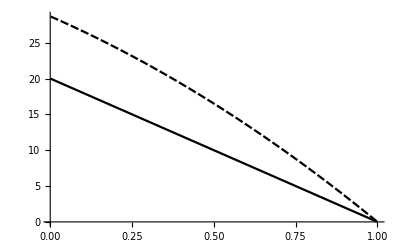

```mathematica
Plot[{P[x]-P[1],P[x]-P[1]+(C1 3)/(α 2)(1-x^2)+α^-c C1(3+2c)/(2a)(x^2-1)},{x,0.001,1},PlotTheme->"Monochrome",PlotLegends->{T["p^\\text{кв}"],T["p\\vert_{\\beta=1}"]},AxesLabel->{T["\\xi"],T["\\nicefrac{p}{\\tau_s}",1.5]}]//Quiet
```

```mathematica
Export["F:\\study_dissertation\\Russian-Phd-LaTeX-Dissertation-Template\\images\\ch2\\pressure_sub3.pdf",%]
```

F:\study_dissertation\Russian-Phd-LaTeX-Dissertation-Template\images\ch2\pressure_sub3.pdf